## Germanium

```mathematica
dataGe=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/EG/eG/``.csv",#],"Table","HeaderLines"->1,"FieldSeparators"->";","NumberPoint"->",",CharacterEncoding->"UTF8"]&/@{"germanium_ccw","germanium_cw"};
```

```mathematica
{t,ang,pyro,sample}=Transpose[First@dataGe](*ccw Ge*);
```

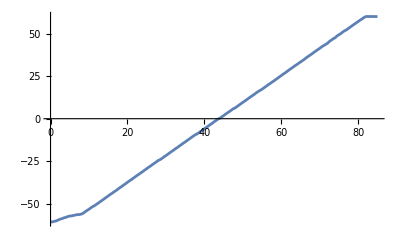

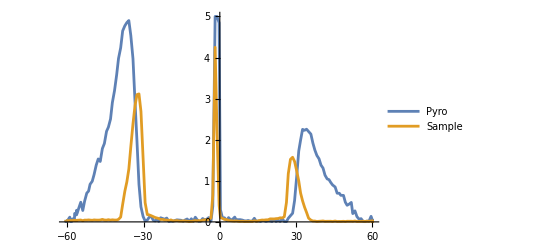

```mathematica
ListLinePlot[Transpose[{t,ang}],PlotRange->All]
ListLinePlot[Transpose[{ang,#}]&/@{pyro,sample},PlotRange->All,PlotLegends->{"Pyro","Sample"}]
```

## Silicon

```mathematica
dataSi=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/EG/eG/``.csv",#],"Table","HeaderLines"->1,"FieldSeparators"->";","NumberPoint"->",",CharacterEncoding->"UTF8"]&/@{"Silicon_ccw","Silicon_cw"};
```

```mathematica
{t2,ang2,pyro2,sample2}=Transpose[First@dataSi](*ccw Si*);
```

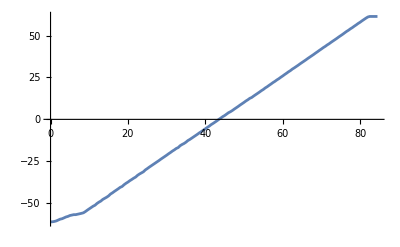

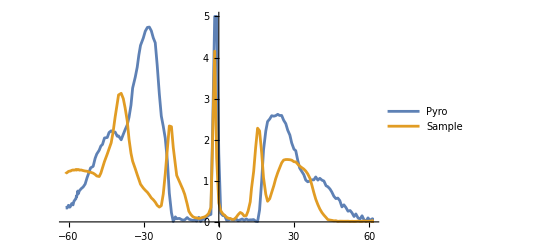

```mathematica
ListLinePlot[Transpose[{t2,ang2}],PlotRange->All]
ListLinePlot[Transpose[{ang2,#}]&/@{pyro2,sample2},PlotRange->All,PlotLegends->{"Pyro","Sample"}]
```

## Lamp spectra

```mathematica
dataLp=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/EG/eG/``.csv",#],"Table","HeaderLines"->1,"FieldSeparators"->";","NumberPoint"->",",CharacterEncoding->"UTF8"]&/@{"Spettro_lampada_ccw","Spettro_lampada_cw"};
```

```mathematica
{t3,ang3,pyro3,sample3}=Transpose[First@dataLp](*ccw Lamp*);
```

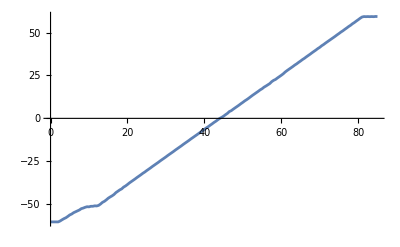

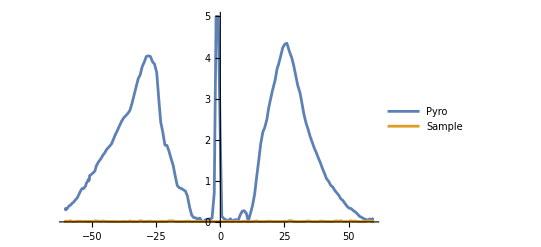

```mathematica
ListLinePlot[Transpose[{t3,ang3}],PlotRange->All]
ListLinePlot[Transpose[{ang3,#}]&/@{pyro3,sample3},PlotRange->All,PlotLegends->{"Pyro","Sample"}]
```